```mathematica
Import["/home/chengling/Research/Project/Cell/glassyDynamics/N4096/productionRuns/p3.825/SACtime_N4096_p3.8250_T0.00100000_waitingTime15000_idx10.nc"]
```

Import::nffil: File /home/chengling/Research/Project/Cell/glassyDynamics/N4096/productionRuns/p3.825/SACtime_N4096_p3.8250_T0.001 not found during Import.

$Failed

```mathematica
testData=Table[Import["/home/chengling/Research/Project/Cell/glassyDynamics/N4096/productionRuns/p3.825/SACtime_N4096_p3.8250_T0.00100000_waitingTime999999_idx"<>ToString[i]<>".nc","Data"],{i,10,19}];
```

Import::nffil: File /home/chengling/Research/Project/Cell/glassyDynamics/N4096/productionRuns/p3.825/SACtime_N4096_p3.8250_T0.00100000_waitingTime999999_idx10.nc not found during Import.

Import::nffil: File /home/chengling/Research/Project/Cell/glassyDynamics/N4096/productionRuns/p3.825/SACtime_N4096_p3.8250_T0.00100000_waitingTime999999_idx11.nc not found during Import.

Import::nffil: File /home/chengling/Research/Project/Cell/glassyDynamics/N4096/productionRuns/p3.825/SACtime_N4096_p3.8250_T0.00100000_waitingTime999999_idx12.nc not found during Import.

General::stop: Further output of Import::nffil will be suppressed during this calculation.

```mathematica
sacfInterp=Table[Interpolation[Transpose[{Normal[testData[[i,2]]],Normal[testData[[i,1]]]}],Method->"Spline"],{i,10}]
```

{InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…]}

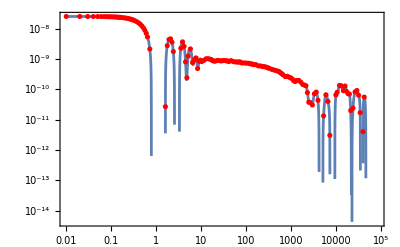

```mathematica
Show[LogLogPlot[sacfInterp[x],{x,0.01,Last[data[[2]]]}],ListLogLogPlot[Table[{data[[2,i]],data[[1,i]]},{i,Length[data[[1]]]}],PlotStyle->Red]]
```

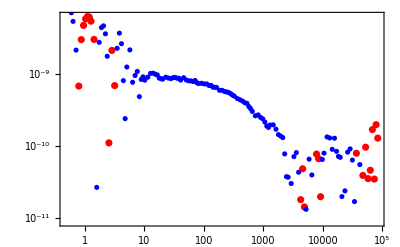

```mathematica
Show[ListLogLogPlot[Table[{data[[2,i]],-data[[1,i]]},{i,Length[data[[1]]]}],PlotStyle->Red],ListLogLogPlot[Table[{data[[2,i]],data[[1,i]]},{i,Length[data[[1]]]}],PlotStyle->Blue]]
```

```mathematica
Table[integralNotInter=Total[(Normal[data[[1,;;85]]][[;;-2]]+Normal[data[[1,;;85]]][[2;;]])/2*Differences[Normal[data[[2,;;85]]]]]
```

1.96174×10^-7

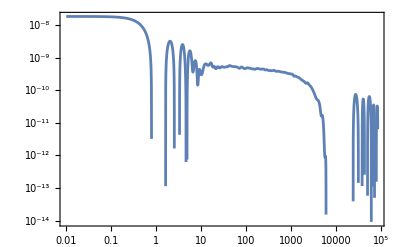

```mathematica
LogLogPlot[sacfInterp[[4]][x],{x,0.01,Last[data[[2]]]}]
```

```mathematica
integral=Table[NIntegrate[sacfInterp[[i]][x],{x,0,6000}],{i,10}]
```

{6.6955×10^-7,8.26495×10^-7,5.83388×10^-7,8.88101×10^-7,2.37819×10^-7,8.67089×10^-7,7.20868×10^-7,2.40596×10^-6,5.49453×10^-7,1.69974×10^-6}

```mathematica
integral*4096/0.0005
```

{5.48496,6.77064,4.77912,7.27532,1.94821,7.10319,5.90535,19.7097,4.50112,13.9243}

```mathematica
Mean[integral*4096/0.0005]
```

7.74018

```mathematica
StandardDeviation[integral*4096/0.0005]/Sqrt[10]
```

1.43541